Data Import

```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/210718_product_diversity"];
```

```mathematica
Get["../algoritm_packages/SingleNetworks-algorithm-package-2.wl"]
(* ?SingleNetworks`* *)
```

```mathematica
datafull=Import["../data/pltcm_manipulated_59604_rev1.csv"];
datafull=Drop[datafull,-4];
```

Data with Sliding Time Windows

```mathematica
x1=Round@Ceiling[Length@datafull/5,1];
{a,b,c,d,e}=Join[Range[x1,Length@datafull,x1]];
data1=Join[{Take[datafull,{1,a}]},Flatten[Table[{Take[datafull,{z[[1]]-x1/2,z[[2]]-x1/2}],Take[datafull,{z[[1]],z[[2]]}]},{z,
Partition[{a,b,c,d,e},2,1]}],1]];
win1=Length@data1;
```

```mathematica
x2=Round@Ceiling[Length@datafull/10,1];
{a,b,c,d,e,f,g,h,i,j}=Join[Range[x2,Length@datafull,x2]];
data2=Join[{Take[datafull,{1,a}]},Flatten[Table[{Take[datafull,{z[[1]]-x2/2,z[[2]]-x2/2}],Take[datafull,{z[[1]],z[[2]]}]},{z,
Partition[{a,b,c,d,e,f,g,h,i,j},2,1]}],1]];
win2=Length@data2;
```

Investigation of Constraints Impact in Time Windows

Fixed Step Size Networks

Width Feature

```mathematica
step11=11;
step12=11;
```

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedstep1=snetworkdatabinnedintimewindows[data1,9,step11,win1];]
```

{12.9352,Null}

```mathematica
graphsandnodenumbers1=Table[snetworkgraph[widthdataintimewindowsFixedstep1[[1]][[i]],widthdataintimewindowsFixedstep1[[2]][[i]],2,7,400,Green],{i,Range@win1}];
modularityvalues1=Table[N@GraphAssortativity[graphsandnodenumbers1[[i]][[1]],FindGraphCommunities[graphsandnodenumbers1[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers1}];
```

```mathematica
singlerandomgraphsdegfxd1=Table[randomizinggraphdegfxd[i],{i,graphsandnodenumbers1[[All,1]]}];
singlerandomerdrenmodularityvalues1=Table[N@GraphAssortativity[singlerandomgraphsdegfxd1[[i]],FindGraphCommunities[singlerandomgraphsdegfxd1[[i]]],"Normalized"->False],{i,Length@singlerandomgraphsdegfxd1}];
singlerandomgraphscomm1=Table[randomizinggraphmod[i],{i,graphsandnodenumbers1[[All,1]]}];
singlerandomcommmodularityvalues1=Table[N@GraphAssortativity[singlerandomgraphscomm1[[i]],FindGraphCommunities[singlerandomgraphscomm1[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm1}];
```

```mathematica
AbsoluteTiming[Zscoresmodularity1=Table[zscorefunctionfortwonullmodels[i],{i,graphsandnodenumbers1[[All,1]]}];]
```

{305.362,Null}

```mathematica
bucketnode11=graphsandnodenumbers1[[All,2]]
```

{78,81,79,79,83,80,80,84,85}

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedstep2=snetworkdatabinnedintimewindows[data2,9,step12,win2];]
```

{17.3232,Null}

```mathematica
graphsandnodenumbers12=Table[snetworkgraph[widthdataintimewindowsFixedstep2[[1]][[i]],widthdataintimewindowsFixedstep2[[2]][[i]],2,7,400,Green],{i,Range@win2}];
modularityvalues12=Table[N@GraphAssortativity[graphsandnodenumbers12[[i]][[1]],FindGraphCommunities[graphsandnodenumbers12[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers12}];
```

```mathematica
singlerandomgraphsdegfxd12=Table[randomizinggraphdegfxd[i],{i,graphsandnodenumbers12[[All,1]]}];
singlerandomerdrenmodularityvalues12=Table[N@GraphAssortativity[singlerandomgraphsdegfxd12[[i]],FindGraphCommunities[singlerandomgraphsdegfxd12[[i]]],"Normalized"->False],{i,Length@singlerandomgraphsdegfxd12}];
singlerandomgraphscomm12=Table[randomizinggraphmod[i],{i,graphsandnodenumbers12[[All,1]]}];
singlerandomcommmodularityvalues12=Table[N@GraphAssortativity[singlerandomgraphscomm12[[i]],FindGraphCommunities[singlerandomgraphscomm12[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm12}];
```

```mathematica
AbsoluteTiming[Zscoresmodularity12=Table[zscorefunctionfortwonullmodels[i],{i,graphsandnodenumbers12[[All,1]]}];]
```

{644.941,Null}

```mathematica
bucketnode12=graphsandnodenumbers12[[All,2]]
```

{73,74,77,77,77,77,75,72,78,81,77,78,75,79,78,80,82,82,84}

```mathematica
(* Cases[p1,{___,c_Directive,__Line}:>ColorConvert[c,RGBColor],Infinity]//InputForm *)
```

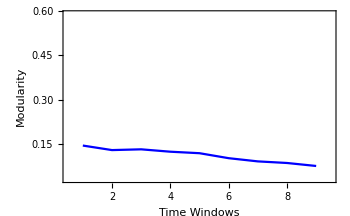
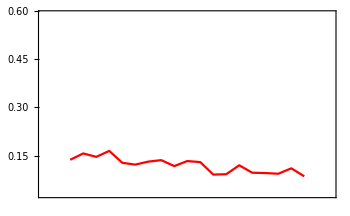
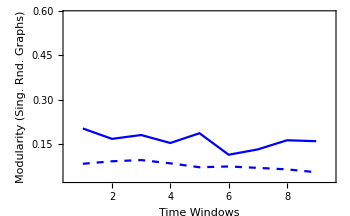
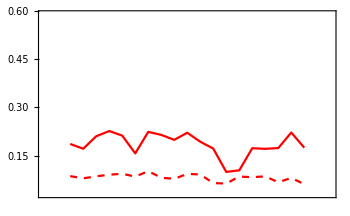
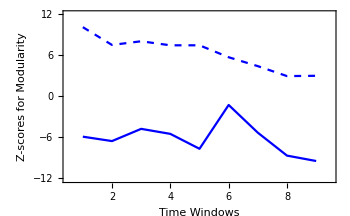
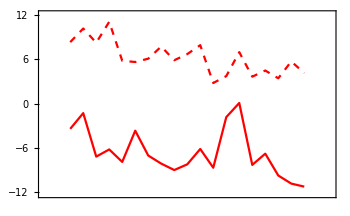

```mathematica
modularityvaluestimewinbig=modularityvalues1;
modularityvaluestimewinsmall=modularityvalues12;
randommodtimewinbigdegreefxd=singlerandomerdrenmodularityvalues1;
randommodtimewinbigcomm=singlerandomcommmodularityvalues1;
randommodtimewinsmalldegreefxd=singlerandomerdrenmodularityvalues12;
randommodtimewinsmallcomm=singlerandomcommmodularityvalues12;
Zscoretimewinbig=Zscoresmodularity1;
Zscoretimewinsmall=Zscoresmodularity12;
modularityplotrange={0.03,0.59};
(*MinMax[{modularityvalues1,singlerandomcommmodularityvalues1,singlerandomerdrenmodularityvalues1,modularityvalues12}]*)
padding=38;
Row[{Overlay[{ListLinePlot[Thread[{Range@win1,modularityvaluestimewinbig}],Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0.5,win1+0.5},modularityplotrange}],ListLinePlot[Thread[{Range@win2,modularityvaluestimewinsmall}],Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{-1,win2+2},modularityplotrange}]}],
Row[{Overlay[{ListLinePlot[{Thread[{Range@win1,randommodtimewinbigdegreefxd}],Thread[{Range@win1,randommodtimewinbigcomm}]},Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity (Sing. Rnd. Graphs)",None},{Style["Time Windows",Blue],None}},PlotStyle->{{Dashed,Blue},Blue},ImageSize->350,PlotRange->{{0.5,win1+0.5},modularityplotrange}],ListLinePlot[{Thread[{Range@win2,randommodtimewinsmalldegreefxd}],Thread[{Range@win2,randommodtimewinsmallcomm}]},Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->{{Dashed,Red},Red},ImageSize->350,PlotRange->{{-1,win2+2},modularityplotrange}]}],
Overlay[{ListLinePlot[{Thread[{Range@win1,Zscoretimewinbig[[All,1]]}],Thread[{Range@win1,Zscoretimewinbig[[All,2]]}]},Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-scores for Modularity",None},{Style["Time Windows",Blue],None}},PlotStyle->{{Dashed,Blue},Blue},ImageSize->350,PlotRange->{{0.5,win1+0.5},MinMax[Flatten[{Zscoretimewinbig,Zscoretimewinsmall}],1]}],ListLinePlot[{Thread[{Range@win2,Zscoretimewinsmall[[All,1]]}],Thread[{Range@win2,Zscoretimewinsmall[[All,2]]}]},Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->{{Dashed,Red},Red},ImageSize->350,PlotRange->{{-1,win2+2},MinMax[Flatten[{Zscoretimewinbig,Zscoretimewinsmall}],1]}]}]}],LineLegend[{Dashed,Black},{"Degrees Fixed N.M.","Modularity N.M."},LegendMargins->0,LegendMarkerSize->{20,20}],Spacer@0.1}]
```

Thickness Feature

```mathematica
step21=0.05;
step22=0.05;
```

```mathematica
AbsoluteTiming[thicknessdataintimewindowsFixedstep1=snetworkdatabinnedintimewindows[data1,10,step21,win1];]
```

{21.5249,Null}

```mathematica
graphsandnodenumbers2=Table[snetworkgraph[thicknessdataintimewindowsFixedstep1[[1]][[i]],thicknessdataintimewindowsFixedstep1[[2]][[i]],2,7,400,RGBColor[0.1,0.5,1.]],{i,Range@win1}];
modularityvalues2=Table[N@GraphAssortativity[graphsandnodenumbers2[[i]][[1]],FindGraphCommunities[graphsandnodenumbers2[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers2}];
```

```mathematica
singlerandomgraphsdegfxd2=Table[randomizinggraphdegfxd[i],{i,graphsandnodenumbers2[[All,1]]}];
singlerandomerdrenmodularityvalues2=Table[N@GraphAssortativity[singlerandomgraphsdegfxd2[[i]],FindGraphCommunities[singlerandomgraphsdegfxd2[[i]]],"Normalized"->False],{i,Length@singlerandomgraphsdegfxd2}];
singlerandomgraphscomm2=Table[randomizinggraphmod[i],{i,graphsandnodenumbers2[[All,1]]}];
singlerandomcommmodularityvalues2=Table[N@GraphAssortativity[singlerandomgraphscomm2[[i]],FindGraphCommunities[singlerandomgraphscomm2[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm2}];
```

```mathematica
AbsoluteTiming[Zscoresmodularity2=Table[zscorefunctionfortwonullmodels[i],{i,graphsandnodenumbers2[[All,1]]}];]
```

{228.429,Null}

```mathematica
bucketnode21=graphsandnodenumbers2[[All,2]]
```

{67,68,70,68,74,74,76,75,73}

```mathematica
AbsoluteTiming[thicknessdataintimewindowsFixedstep2=snetworkdatabinnedintimewindows[data2,10,step22,win2];]
```

{18.1963,Null}

```mathematica
graphsandnodenumbers22=Table[snetworkgraph[thicknessdataintimewindowsFixedstep2[[1]][[i]],thicknessdataintimewindowsFixedstep2[[2]][[i]],2,7,400,RGBColor[0.1,0.5,1.]],{i,Range@win2}];
modularityvalues22=Table[N@GraphAssortativity[graphsandnodenumbers22[[i]][[1]],FindGraphCommunities[graphsandnodenumbers22[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers22}];
```

```mathematica
singlerandomgraphsdegfxd22=Table[randomizinggraphdegfxd[i],{i,graphsandnodenumbers22[[All,1]]}];
singlerandomerdrenmodularityvalues22=Table[N@GraphAssortativity[singlerandomgraphsdegfxd22[[i]],FindGraphCommunities[singlerandomgraphsdegfxd22[[i]]],"Normalized"->False],{i,Length@singlerandomgraphsdegfxd22}];
singlerandomgraphscomm22=Table[randomizinggraphmod[i],{i,graphsandnodenumbers22[[All,1]]}];
singlerandomcommmodularityvalues22=Table[N@GraphAssortativity[singlerandomgraphscomm22[[i]],FindGraphCommunities[singlerandomgraphscomm22[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm22}];
```

```mathematica
AbsoluteTiming[Zscoresmodularity22=Table[zscorefunctionfortwonullmodels[i],{i,graphsandnodenumbers22[[All,1]]}];]
```

{463.41,Null}

```mathematica
bucketnode22=graphsandnodenumbers22[[All,2]]
```

{66,67,66,67,65,66,67,68,67,71,74,74,71,70,75,74,69,71,71}

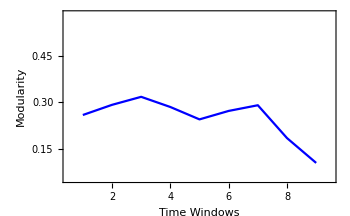
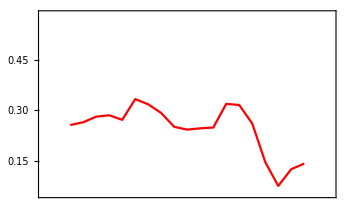
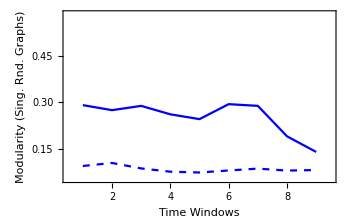
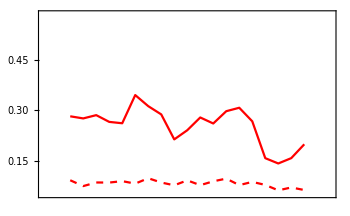
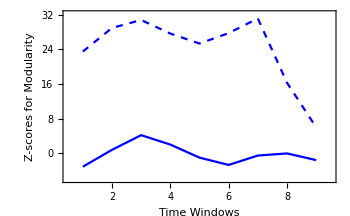
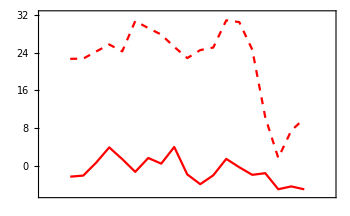

```mathematica
modularityvaluestimewinbig=modularityvalues2;
modularityvaluestimewinsmall=modularityvalues22;
randommodtimewinbigdegreefxd=singlerandomerdrenmodularityvalues2;
randommodtimewinbigcomm=singlerandomcommmodularityvalues2;
randommodtimewinsmalldegreefxd=singlerandomerdrenmodularityvalues22;
randommodtimewinsmallcomm=singlerandomcommmodularityvalues22;
Zscoretimewinbig=Zscoresmodularity2;
Zscoretimewinsmall=Zscoresmodularity22;
modularityplotrange={0.05246,0.584368};
(*MinMax[{modularityvalues1,singlerandomcommmodularityvalues1,singlerandomerdrenmodularityvalues1,modularityvalues12}]*)
padding=38;
Row[{Overlay[{ListLinePlot[Thread[{Range@win1,modularityvaluestimewinbig}],Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0.5,win1+0.5},modularityplotrange}],ListLinePlot[Thread[{Range@win2,modularityvaluestimewinsmall}],Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{-1,win2+2},modularityplotrange}]}],
Row[{Overlay[{ListLinePlot[{Thread[{Range@win1,randommodtimewinbigdegreefxd}],Thread[{Range@win1,randommodtimewinbigcomm}]},Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity (Sing. Rnd. Graphs)",None},{Style["Time Windows",Blue],None}},PlotStyle->{{Dashed,Blue},Blue},ImageSize->350,PlotRange->{{0.5,win1+0.5},modularityplotrange}],ListLinePlot[{Thread[{Range@win2,randommodtimewinsmalldegreefxd}],Thread[{Range@win2,randommodtimewinsmallcomm}]},Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->{{Dashed,Red},Red},ImageSize->350,PlotRange->{{-1,win2+2},modularityplotrange}]}],
Overlay[{ListLinePlot[{Thread[{Range@win1,Zscoretimewinbig[[All,1]]}],Thread[{Range@win1,Zscoretimewinbig[[All,2]]}]},Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-scores for Modularity",None},{Style["Time Windows",Blue],None}},PlotStyle->{{Dashed,Blue},Blue},ImageSize->350,PlotRange->{{0.5,win1+0.5},MinMax[Flatten[{Zscoretimewinbig,Zscoretimewinsmall}],1]}],ListLinePlot[{Thread[{Range@win2,Zscoretimewinsmall[[All,1]]}],Thread[{Range@win2,Zscoretimewinsmall[[All,2]]}]},Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->{{Dashed,Red},Red},ImageSize->350,PlotRange->{{-1,win2+2},MinMax[Flatten[{Zscoretimewinbig,Zscoretimewinsmall}],1]}]}]}],LineLegend[{Dashed,Black},{"Degrees Fixed N.M.","Modularity N.M."},LegendMargins->0,LegendMarkerSize->{20,20}],Spacer@0.1}]
```

Fixed Bucket Size Networks

Width Feature

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedbucket1=snetworkdatafxdbucketintimewindows[data1,9,bucketnode11,win1];]
```

{2.32047,Null}

```mathematica
bucketsize3=Flatten@widthdataintimewindowsFixedbucket1[[4]]
```

{153,148,151,151,144,150,150,142,141}

```mathematica
graphsandnodenumbers3=Table[snetworkgraph[widthdataintimewindowsFixedbucket1[[1]][[i]],widthdataintimewindowsFixedbucket1[[2]][[i]],1.5,7,400,Green],{i,Range@win1}];
modularityvalues3=Table[N@GraphAssortativity[graphsandnodenumbers3[[i]][[1]],FindGraphCommunities[graphsandnodenumbers3[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers3}];
```

```mathematica
singlerandomgraphsdegfxd3=Table[randomizinggraphdegfxd[i],{i,graphsandnodenumbers3[[All,1]]}];
singlerandomerdrenmodularityvalues3=Table[N@GraphAssortativity[singlerandomgraphsdegfxd3[[i]],FindGraphCommunities[singlerandomgraphsdegfxd3[[i]]],"Normalized"->False],{i,Length@singlerandomgraphsdegfxd3}];
singlerandomgraphscomm3=Table[randomizinggraphmod[i],{i,graphsandnodenumbers3[[All,1]]}];
singlerandomcommmodularityvalues3=Table[N@GraphAssortativity[singlerandomgraphscomm3[[i]],FindGraphCommunities[singlerandomgraphscomm3[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm3}];
```

```mathematica
AbsoluteTiming[Zscoresmodularity3=Table[zscorefunctionfortwonullmodels[i],{i,graphsandnodenumbers3[[All,1]]}];]
```

{280.321,Null}

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedbucket2=snetworkdatafxdbucketintimewindows[data2,9,bucketnode12,win2];]
```

{2.41113,Null}

```mathematica
bucketsize32=Flatten@widthdataintimewindowsFixedbucket2[[4]]
```

{82,81,78,78,78,78,80,83,77,74,78,77,80,76,77,75,73,73,71}

```mathematica
graphsandnodenumbers32=Table[snetworkgraph[widthdataintimewindowsFixedbucket2[[1]][[i]],widthdataintimewindowsFixedbucket2[[2]][[i]],1.5,7,400,Green],{i,Range@win2}];
modularityvalues32=Table[N@GraphAssortativity[graphsandnodenumbers32[[i]][[1]],FindGraphCommunities[graphsandnodenumbers32[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers32}];
```

```mathematica
singlerandomgraphsdegfxd32=Table[randomizinggraphdegfxd[i],{i,graphsandnodenumbers32[[All,1]]}];
singlerandomerdrenmodularityvalues32=Table[N@GraphAssortativity[singlerandomgraphsdegfxd32[[i]],FindGraphCommunities[singlerandomgraphsdegfxd32[[i]]],"Normalized"->False],{i,Length@singlerandomgraphsdegfxd32}];
singlerandomgraphscomm32=Table[randomizinggraphmod[i],{i,graphsandnodenumbers32[[All,1]]}];
singlerandomcommmodularityvalues32=Table[N@GraphAssortativity[singlerandomgraphscomm32[[i]],FindGraphCommunities[singlerandomgraphscomm32[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm32}];
```

```mathematica
AbsoluteTiming[Zscoresmodularity32=Table[zscorefunctionfortwonullmodels[i],{i,graphsandnodenumbers32[[All,1]]}];]
```

{506.496,Null}

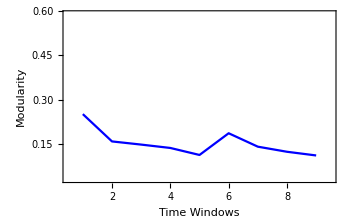
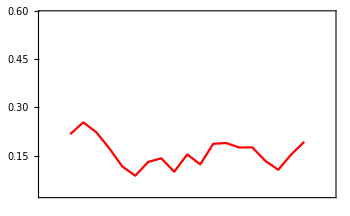
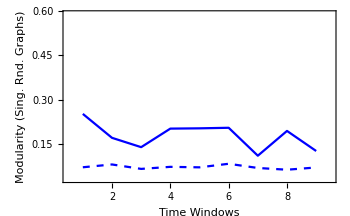
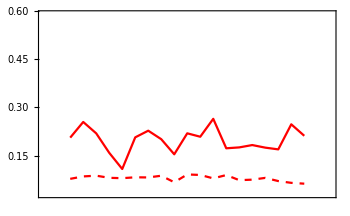
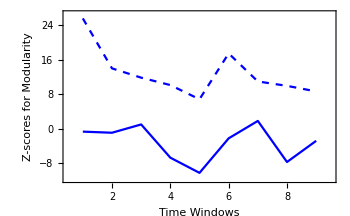
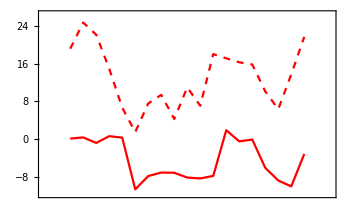

```mathematica
modularityvaluestimewinbig=modularityvalues3;
modularityvaluestimewinsmall=modularityvalues32;
randommodtimewinbigdegreefxd=singlerandomerdrenmodularityvalues3;
randommodtimewinbigcomm=singlerandomcommmodularityvalues3;
randommodtimewinsmalldegreefxd=singlerandomerdrenmodularityvalues32;
randommodtimewinsmallcomm=singlerandomcommmodularityvalues32;
Zscoretimewinbig=Zscoresmodularity3;
Zscoretimewinsmall=Zscoresmodularity32;
modularityplotrange={0.03,0.59};
(*MinMax[{modularityvalues1,singlerandomcommmodularityvalues1,singlerandomerdrenmodularityvalues1,modularityvalues12}]*)
padding=38;
Row[{Overlay[{ListLinePlot[Thread[{Range@win1,modularityvaluestimewinbig}],Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0.5,win1+0.5},modularityplotrange}],ListLinePlot[Thread[{Range@win2,modularityvaluestimewinsmall}],Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{-1,win2+2},modularityplotrange}]}],
Row[{Overlay[{ListLinePlot[{Thread[{Range@win1,randommodtimewinbigdegreefxd}],Thread[{Range@win1,randommodtimewinbigcomm}]},Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity (Sing. Rnd. Graphs)",None},{Style["Time Windows",Blue],None}},PlotStyle->{{Dashed,Blue},Blue},ImageSize->350,PlotRange->{{0.5,win1+0.5},modularityplotrange}],ListLinePlot[{Thread[{Range@win2,randommodtimewinsmalldegreefxd}],Thread[{Range@win2,randommodtimewinsmallcomm}]},Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->{{Dashed,Red},Red},ImageSize->350,PlotRange->{{-1,win2+2},modularityplotrange}]}],
Overlay[{ListLinePlot[{Thread[{Range@win1,Zscoretimewinbig[[All,1]]}],Thread[{Range@win1,Zscoretimewinbig[[All,2]]}]},Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-scores for Modularity",None},{Style["Time Windows",Blue],None}},PlotStyle->{{Dashed,Blue},Blue},ImageSize->350,PlotRange->{{0.5,win1+0.5},MinMax[Flatten[{Zscoretimewinbig,Zscoretimewinsmall}],1]}],ListLinePlot[{Thread[{Range@win2,Zscoretimewinsmall[[All,1]]}],Thread[{Range@win2,Zscoretimewinsmall[[All,2]]}]},Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->{{Dashed,Red},Red},ImageSize->350,PlotRange->{{-1,win2+2},MinMax[Flatten[{Zscoretimewinbig,Zscoretimewinsmall}],1]}]}]}],LineLegend[{Dashed,Black},{"Degrees Fixed N.M.","Modularity N.M."},LegendMargins->0,LegendMarkerSize->{20,20}],Spacer@0.1}]
```

Thickness Feature

```mathematica
AbsoluteTiming[thicknessdataintimewindowsFixedbucket1=snetworkdatafxdbucketintimewindows[data1,10,bucketnode21,win1];]
```

{2.24456,Null}

```mathematica
bucketsize4=Flatten@thicknessdataintimewindowsFixedbucket1[[4]]
```

{178,176,171,176,162,162,157,159,164}

```mathematica
graphsandnodenumbers4=Table[snetworkgraph[thicknessdataintimewindowsFixedbucket1[[1]][[i]],thicknessdataintimewindowsFixedbucket1[[2]][[i]],1.5,7,400,RGBColor[0.1,0.5,1.]],{i,Range@win1}];
modularityvalues4=Table[N@GraphAssortativity[graphsandnodenumbers4[[i]][[1]],FindGraphCommunities[graphsandnodenumbers4[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers4}];
```

```mathematica
singlerandomgraphsdegfxd4=Table[randomizinggraphdegfxd[i],{i,graphsandnodenumbers4[[All,1]]}];
singlerandomerdrenmodularityvalues4=Table[N@GraphAssortativity[singlerandomgraphsdegfxd4[[i]],FindGraphCommunities[singlerandomgraphsdegfxd4[[i]]],"Normalized"->False],{i,Length@singlerandomgraphsdegfxd4}];
singlerandomgraphscomm4=Table[randomizinggraphmod[i],{i,graphsandnodenumbers4[[All,1]]}];
singlerandomcommmodularityvalues4=Table[N@GraphAssortativity[singlerandomgraphscomm4[[i]],FindGraphCommunities[singlerandomgraphscomm4[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm4}];
```

```mathematica
AbsoluteTiming[Zscoresmodularity4=Table[zscorefunctionfortwonullmodels[i],{i,graphsandnodenumbers4[[All,1]]}];]
```

{181.181,Null}

```mathematica
AbsoluteTiming[thicknessdataintimewindowsFixedbucket2=snetworkdatafxdbucketintimewindows[data2,10,bucketnode22,win2];]
```

{2.07623,Null}

```mathematica
bucketsize42=Flatten@thicknessdataintimewindowsFixedbucket2[[4]]
```

{91,89,91,89,92,91,89,88,89,84,81,81,84,86,80,81,87,84,84}

```mathematica
graphsandnodenumbers42=Table[snetworkgraph[thicknessdataintimewindowsFixedbucket2[[1]][[i]],thicknessdataintimewindowsFixedbucket2[[2]][[i]],1.5,7,400,RGBColor[0.1,0.5,1.]],{i,Range@win2}];
modularityvalues42=Table[N@GraphAssortativity[graphsandnodenumbers42[[i]][[1]],FindGraphCommunities[graphsandnodenumbers42[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers42}];
```

```mathematica
singlerandomgraphsdegfxd42=Table[randomizinggraphdegfxd[i],{i,graphsandnodenumbers42[[All,1]]}];
singlerandomerdrenmodularityvalues42=Table[N@GraphAssortativity[singlerandomgraphsdegfxd42[[i]],FindGraphCommunities[singlerandomgraphsdegfxd42[[i]]],"Normalized"->False],{i,Length@singlerandomgraphsdegfxd42}];
singlerandomgraphscomm42=Table[randomizinggraphmod[i],{i,graphsandnodenumbers42[[All,1]]}];
singlerandomcommmodularityvalues42=Table[N@GraphAssortativity[singlerandomgraphscomm42[[i]],FindGraphCommunities[singlerandomgraphscomm42[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm42}];
```

```mathematica
AbsoluteTiming[Zscoresmodularity42=Table[zscorefunctionfortwonullmodels[i],{i,graphsandnodenumbers42[[All,1]]}];]
```

{345.672,Null}

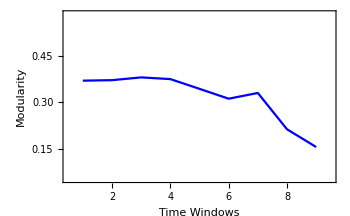
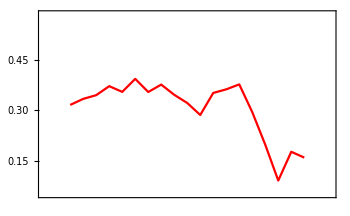
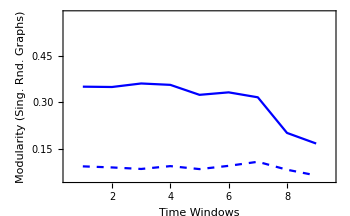
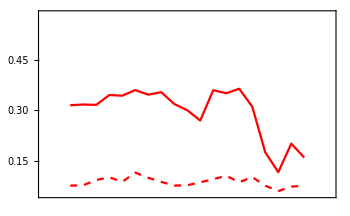
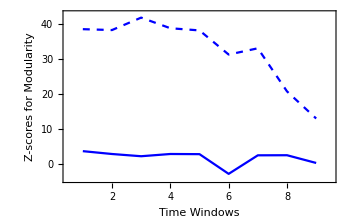
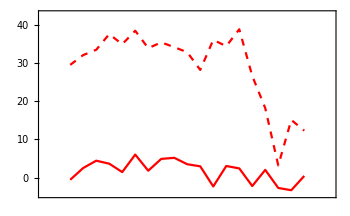

```mathematica
modularityvaluestimewinbig=modularityvalues4;
modularityvaluestimewinsmall=modularityvalues42;
randommodtimewinbigdegreefxd=singlerandomerdrenmodularityvalues4;
randommodtimewinbigcomm=singlerandomcommmodularityvalues4;
randommodtimewinsmalldegreefxd=singlerandomerdrenmodularityvalues42;
randommodtimewinsmallcomm=singlerandomcommmodularityvalues42;
Zscoretimewinbig=Zscoresmodularity4;
Zscoretimewinsmall=Zscoresmodularity42/.ComplexInfinity->0;
modularityplotrange={0.05246,0.584368};
(*MinMax[{modularityvalues1,singlerandomcommmodularityvalues1,singlerandomerdrenmodularityvalues1,modularityvalues12}]*)
padding=38;
Row[{Overlay[{ListLinePlot[Thread[{Range@win1,modularityvaluestimewinbig}],Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0.5,win1+0.5},modularityplotrange}],ListLinePlot[Thread[{Range@win2,modularityvaluestimewinsmall}],Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{-1,win2+2},modularityplotrange}]}],
Row[{Overlay[{ListLinePlot[{Thread[{Range@win1,randommodtimewinbigdegreefxd}],Thread[{Range@win1,randommodtimewinbigcomm}]},Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity (Sing. Rnd. Graphs)",None},{Style["Time Windows",Blue],None}},PlotStyle->{{Dashed,Blue},Blue},ImageSize->350,PlotRange->{{0.5,win1+0.5},modularityplotrange}],ListLinePlot[{Thread[{Range@win2,randommodtimewinsmalldegreefxd}],Thread[{Range@win2,randommodtimewinsmallcomm}]},Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->{{Dashed,Red},Red},ImageSize->350,PlotRange->{{-1,win2+2},modularityplotrange}]}],
Overlay[{ListLinePlot[{Thread[{Range@win1,Zscoretimewinbig[[All,1]]}],Thread[{Range@win1,Zscoretimewinbig[[All,2]]}]},Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-scores for Modularity",None},{Style["Time Windows",Blue],None}},PlotStyle->{{Dashed,Blue},Blue},ImageSize->350,PlotRange->{{0.5,win1+0.5},MinMax[Flatten[{Zscoretimewinbig,Zscoretimewinsmall}],1]}],ListLinePlot[{Thread[{Range@win2,Zscoretimewinsmall[[All,1]]}],Thread[{Range@win2,Zscoretimewinsmall[[All,2]]}]},Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->{{Dashed,Red},Red},ImageSize->350,PlotRange->{{-1,win2+2},MinMax[Flatten[{Zscoretimewinbig,Zscoretimewinsmall}],1]}]}]}],LineLegend[{Dashed,Black},{"Degrees Fixed N.M.","Modularity N.M."},LegendMargins->0,LegendMarkerSize->{20,20}],Spacer@0.1}]
```

node numbers should be equal for two different network approaches (fixed step size and fixed bucket size) for the same data.

```mathematica
Print[Style[{"Width Network Nodes for large timewindow - Fixed StepSize",step12},Blue],graphsandnodenumbers1[[All,2]]]
Print[Style[{"Width Network Nodes for large timewindow - Fixed BucketSize",bucketsize3},Blue],graphsandnodenumbers3[[All,2]]]
Print[Style[{"Width Network Nodes for narrow timewindow - Fixed StepSize",step12},Red],graphsandnodenumbers12[[All,2]]]
Print[Style[{"Width Network Nodes for narrow timewindow - Fixed BucketSize",bucketsize32},Red],graphsandnodenumbers32[[All,2]]]

Print[Style[{"Thickness Network Nodes for large timewindow - Fixed StepSize",step21},Blue],graphsandnodenumbers2[[All,2]]]
Print[Style[{"Thickness Network Nodes for large timewindow - Fixed BucketSize",bucketsize4},Blue],graphsandnodenumbers4[[All,2]]]
Print[Style[{"Thickness Network Nodes for narrow timewindow - Fixed StepSize",step22},Red],graphsandnodenumbers22[[All,2]]]
Print[Style[{"Thickness Network Nodes for narrow timewindow - Fixed BucketSize",bucketsize42},Red],graphsandnodenumbers42[[All,2]]]
```

{Width Network Nodes for large timewindow - Fixed StepSize,11}{78,81,79,79,83,80,80,84,85}

{Width Network Nodes for large timewindow - Fixed BucketSize,{153,148,151,151,144,150,150,142,141}}{78,81,79,79,83,80,80,84,85}

{Width Network Nodes for narrow timewindow - Fixed StepSize,11}{73,74,77,77,77,77,75,72,78,81,77,78,75,79,78,80,82,82,84}

{Width Network Nodes for narrow timewindow - Fixed BucketSize,{82,81,78,78,78,78,80,83,77,74,78,77,80,76,77,75,73,73,71}}{73,74,77,77,77,77,75,72,78,81,77,78,75,79,78,80,82,82,84}

{Thickness Network Nodes for large timewindow - Fixed StepSize,0.05}{67,68,70,68,74,74,76,75,73}

{Thickness Network Nodes for large timewindow - Fixed BucketSize,{178,176,171,176,162,162,157,159,164}}{67,68,70,68,74,74,76,75,73}

{Thickness Network Nodes for narrow timewindow - Fixed StepSize,0.05}{66,67,66,67,65,66,67,68,67,71,74,74,71,70,75,74,69,71,71}

{Thickness Network Nodes for narrow timewindow - Fixed BucketSize,{91,89,91,89,92,91,89,88,89,84,81,81,84,86,80,81,87,84,84}}{66,67,66,67,65,66,67,68,67,71,74,74,71,70,75,74,69,71,71}